## Goodness of Fit Test

```mathematica
data=Import["E:\\2011-2012 ~ UIUC\\SPRING 2012\\CEE 512 - Logistics Systems Analysis\\Project\\Demand2.xls"]
```

{{{0.,6.,0.,20.,0.},{0.,0.,4.,0.,8.},{17.,6.,0.,0.,4.},{0.,4.,0.,40.,8.},{16.,0.,0.,12.,0.},{12.,4.,4.,12.,0.},{0.,2.,8.,12.,0.},{12.,2.,4.,16.,0.},{12.,6.,0.,4.,0.},{0.,4.,0.,12.,0.},{0.,0.,0.,16.,0.},{0.,2.,16.,24.,0.},{12.,0.,0.,12.,0.},{0.,0.,0.,0.,0.},{12.,2.,0.,4.,0.},{8.,2.,4.,12.,0.},{0.,0.,4.,8.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,16.,0.},{4.,2.,4.,16.,0.},{0.,4.,4.,4.,4.},{0.,2.,0.,8.,0.},{8.,0.,0.,16.,0.},{16.,2.,4.,8.,0.},{8.,0.,8.,0.,0.},{8.,2.,12.,0.,0.},{20.,0.,20.,0.,0.},{0.,0.,0.,0.,0.},{8.,2.,8.,0.,0.},{0.,0.,12.,0.,0.},{0.,4.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}},{{}},{{}}}

```mathematica
data=data[[1]]
```

{{0.,6.,0.,20.,0.},{0.,0.,4.,0.,8.},{17.,6.,0.,0.,4.},{0.,4.,0.,40.,8.},{16.,0.,0.,12.,0.},{12.,4.,4.,12.,0.},{0.,2.,8.,12.,0.},{12.,2.,4.,16.,0.},{12.,6.,0.,4.,0.},{0.,4.,0.,12.,0.},{0.,0.,0.,16.,0.},{0.,2.,16.,24.,0.},{12.,0.,0.,12.,0.},{0.,0.,0.,0.,0.},{12.,2.,0.,4.,0.},{8.,2.,4.,12.,0.},{0.,0.,4.,8.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,16.,0.},{4.,2.,4.,16.,0.},{0.,4.,4.,4.,4.},{0.,2.,0.,8.,0.},{8.,0.,0.,16.,0.},{16.,2.,4.,8.,0.},{8.,0.,8.,0.,0.},{8.,2.,12.,0.,0.},{20.,0.,20.,0.,0.},{0.,0.,0.,0.,0.},{8.,2.,8.,0.,0.},{0.,0.,12.,0.,0.},{0.,4.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}

```mathematica
Length[data]
```

36

```mathematica
labels={"VCC - 1", "VFF - 2","VCT - 3", "VBT - 4", "VSBH - 5"};
```

```mathematica
demand=Table[Select[data[[;;,i]],(#≠0&)],{i,5}]//Round;
```

```mathematica
demandFall=Table[Select[data[[1;;17,i]],(#≠0&)],{i,5}]//Round;
```

```mathematica
demandSpring=Table[Select[data[[18;;36,i]],(#≠0&)],{i,5}]//Round;
```

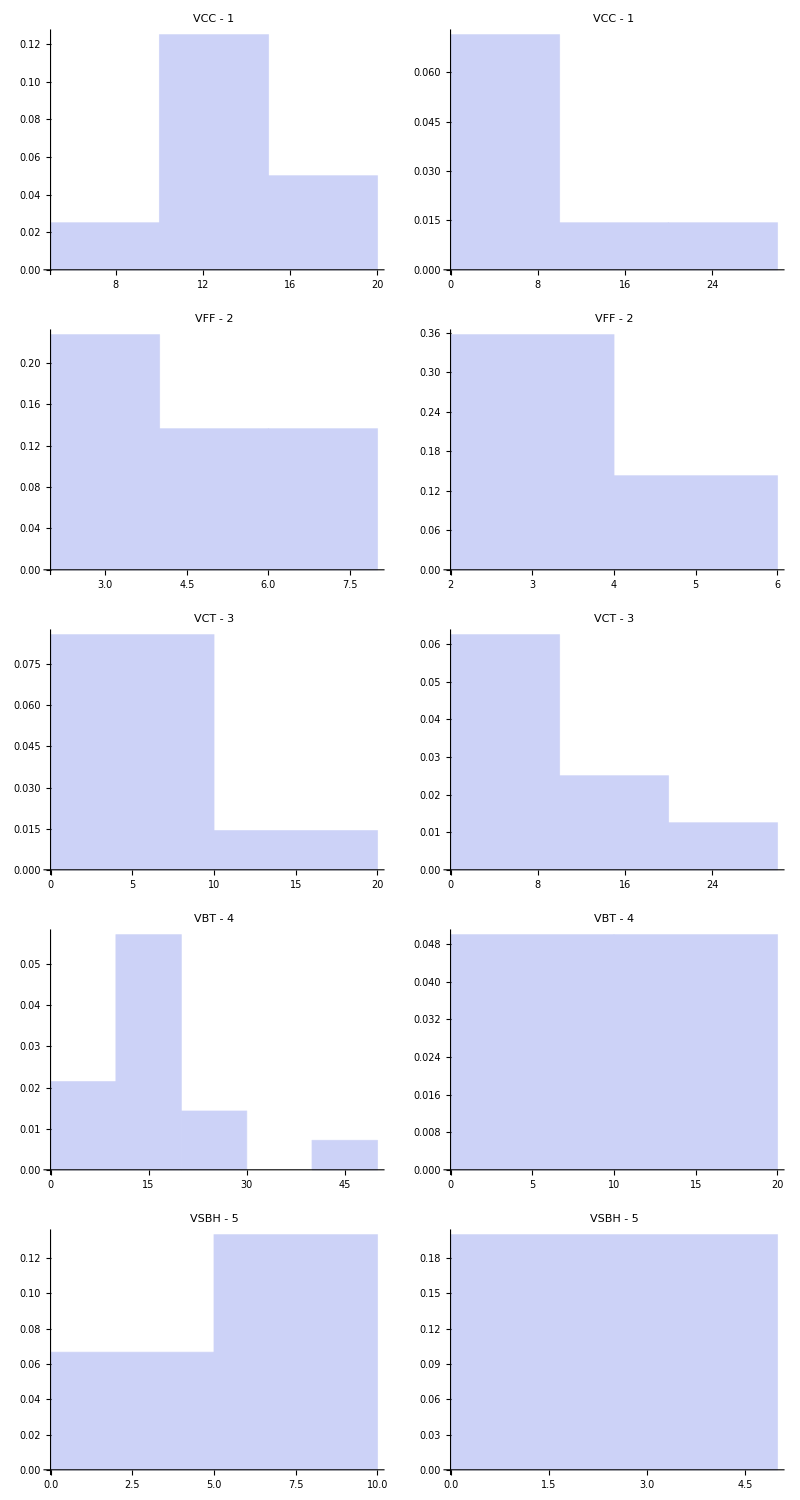

```mathematica
Table[{Histogram[demandFall[[i]],Automatic,"PDF",PlotLabel-> labels[[i]]],
Histogram[demandSpring[[i]],Automatic,"PDF",PlotLabel-> labels[[i]]]},{i,5}]//Grid
```

```mathematica
hist=Table[Histogram[demand[[i]],100,"PDF",PlotLabel-> labels[[i]]],{i,5}];
```

```mathematica
poissondist=Table[EstimatedDistribution[demand[[i]],PoissonDistribution[μ]],{i,5}]
```

{PoissonDistribution[11.5333],PoissonDistribution[3.22222],PoissonDistribution[7.73333],PoissonDistribution[13.6],PoissonDistribution[6.]}

```mathematica
discretePlot=Table[DiscretePlot[PDF[poissondist[[i]],x],{x,Min[demand[[i]]],Max[demand[[i]]]},PlotRange->All,FillingStyle->Thick],{i,5}];
```

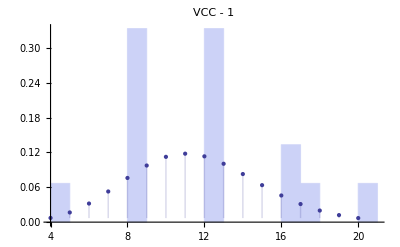
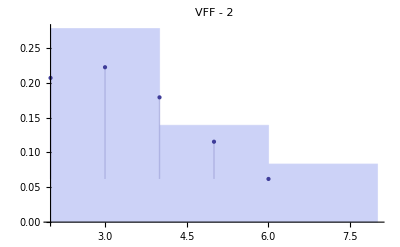
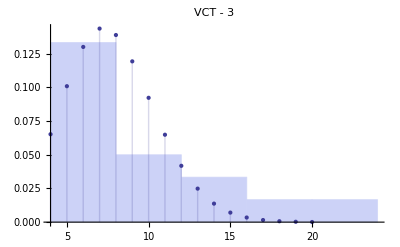
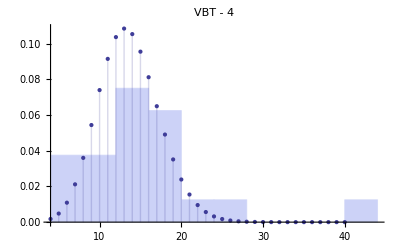
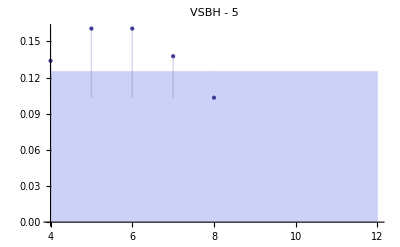

```mathematica
Table[Show[hist[[i]],discretePlot[[i]]],{i,5}]
```

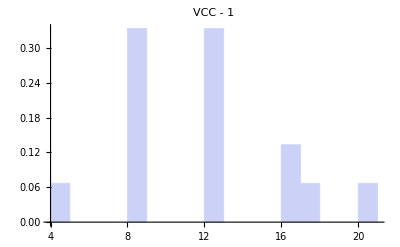
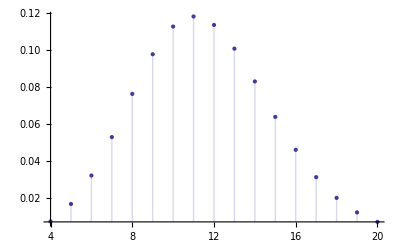
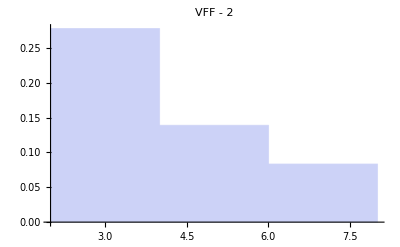
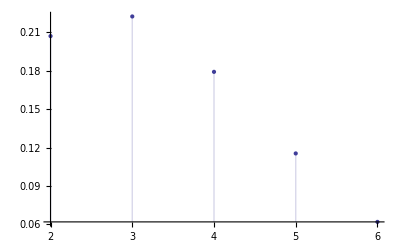
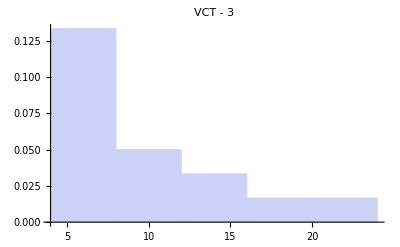
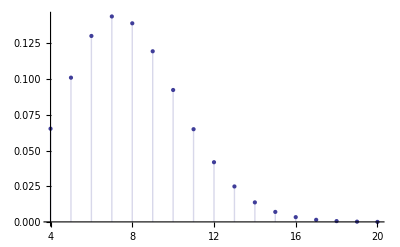
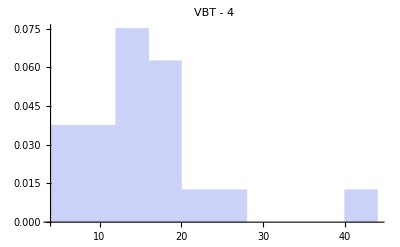
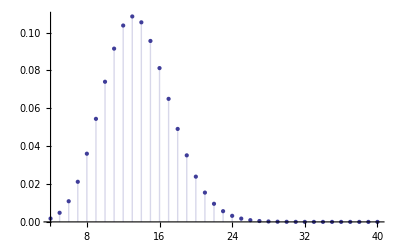

```mathematica
Table[{hist[[i]],discretePlot[[i]]},{i,5}]//Column
```

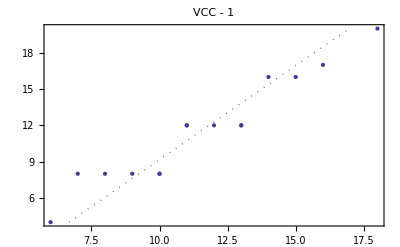
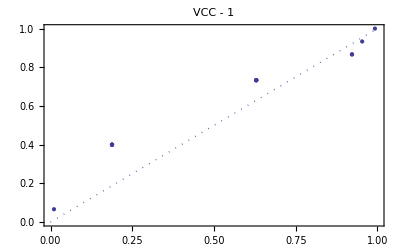
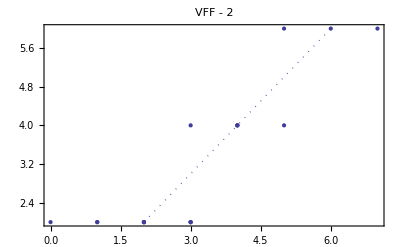
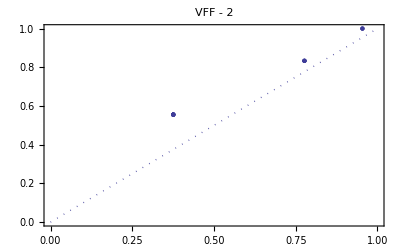
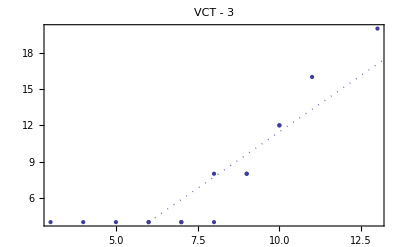
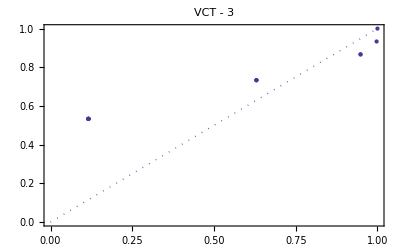
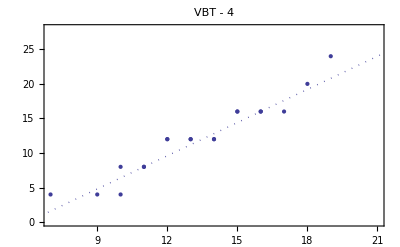
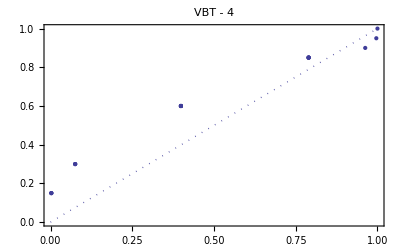

```mathematica
Table[{QuantilePlot[demand[[i]],poissondist[[i]],PlotLabel-> labels[[i]]],ProbabilityPlot[demand[[i]],poissondist[[i]],PlotLabel-> labels[[i]]]},{i,5}]//Column
```

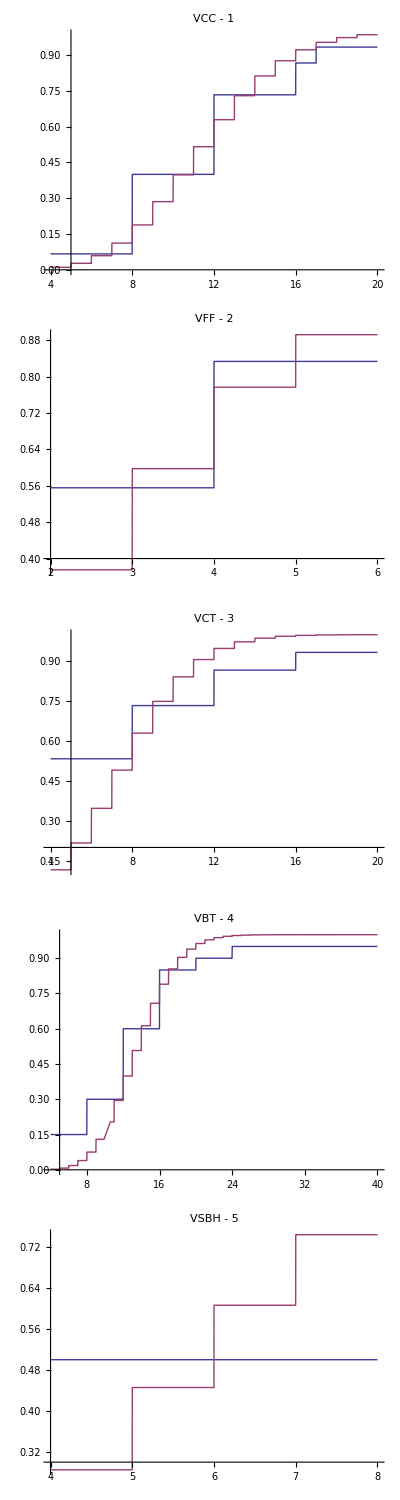

```mathematica
Table[Plot[{CDF[EmpiricalDistribution[demand[[i]]],x],CDF[poissondist[[i]],x]},{x,Min[demand[[i]]],Max[demand[[i]]]},Exclusions->None,PlotLabel-> labels[[i]]],{i,5}]//Column
```

```mathematica
ptest=Table[DistributionFitTest[demand[[i]],PoissonDistribution[μ],"HypothesisTestData"],{i,5}];
```

```mathematica
Table[{labels[[i]],ptest[[i]]["TestDataTable"]},{i,5}]//Column
```

{VCC - 1, | Statistic | P-Value
Pearson χ^2 | 14.1723 | 0.00676489}
{VFF - 2, | Statistic | P-Value
Pearson χ^2 | 21.2312 | 0.000284928}
{VCT - 3, | Statistic | P-Value
Pearson χ^2 | 13.5208 | 0.0089926}
{VBT - 4, | Statistic | P-Value
Pearson χ^2 | 9.05731 | 0.1068}
{VSBH - 5, | Statistic | P-Value
Pearson χ^2 | 3.65858 | 0.160528}

```mathematica
Table[{labels[[i]],ptest[[i]]["TestDataTable"],ptest[[i]]["TestConclusion"]},{i,5}]//Column
```

{VCC - 1, | Statistic | P-Value
Pearson χ^2 | 14.1723 | 0.00676489,The null hypothesis that the data is distributed according to the PoissonDistribution[μ] is rejected at the 5. percent level based on the Pearson χ^2 test.}
{VFF - 2, | Statistic | P-Value
Pearson χ^2 | 21.2312 | 0.000284928,The null hypothesis that the data is distributed according to the PoissonDistribution[μ] is rejected at the 5. percent level based on the Pearson χ^2 test.}
{VCT - 3, | Statistic | P-Value
Pearson χ^2 | 13.5208 | 0.0089926,The null hypothesis that the data is distributed according to the PoissonDistribution[μ] is rejected at the 5. percent level based on the Pearson χ^2 test.}
{VBT - 4, | Statistic | P-Value
Pearson χ^2 | 9.05731 | 0.1068,The null hypothesis that the data is distributed according to the PoissonDistribution[μ] is not rejected at the 5. percent level based on the Pearson χ^2 test.}
{VSBH - 5, | Statistic | P-Value
Pearson χ^2 | 3.65858 | 0.160528,The null hypothesis that the data is distributed according to the PoissonDistribution[μ] is not rejected at the 5. percent level based on the Pearson χ^2 test.}

```mathematica
normaldist=Table[EstimatedDistribution[demand[[i]],NormalDistribution[μ,σ]],{i,5}]
```

{NormalDistribution[11.5333,4.17719],NormalDistribution[3.22222,1.51127],NormalDistribution[7.73333,4.94593],NormalDistribution[13.6,7.93977],NormalDistribution[6.,2.]}

```mathematica
ntest=Table[DistributionFitTest[demand[[i]],NormalDistribution[μ,σ],"HypothesisTestData"],{i,5}];
```

```mathematica
Table[{labels[[i]],ntest[[i]]["TestDataTable"],ntest[[i]]["TestConclusion"]},{i,5}]//Column
```

{VCC - 1, | Statistic | P-Value
Watson U^2 | 0.109722 | 0.062301,The null hypothesis that the data is distributed according to the NormalDistribution[μ,σ] is not rejected at the 5. percent level based on the Watson U^2 test.}
{VFF - 2, | Statistic | P-Value
Watson U^2 | 0.345011 | 0.000434907,The null hypothesis that the data is distributed according to the NormalDistribution[μ,σ] is rejected at the 5. percent level based on the Watson U^2 test.}
{VCT - 3, | Statistic | P-Value
Watson U^2 | 0.242079 | 0.000937337,The null hypothesis that the data is distributed according to the NormalDistribution[μ,σ] is rejected at the 5. percent level based on the Watson U^2 test.}
{VBT - 4, | Statistic | P-Value
Watson U^2 | 0.138776 | 0.0227025,The null hypothesis that the data is distributed according to the NormalDistribution[μ,σ] is rejected at the 5. percent level based on the Watson U^2 test.}
{VSBH - 5, | Statistic | P-Value
Watson U^2 | 0.117551 | 0.0477956,The null hypothesis that the data is distributed according to the NormalDistribution[μ,σ] is rejected at the 5. percent level based on the Watson U^2 test.}